```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
plotsDir= "../../plots/plots-104";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
FileNames[All,"../../runs/Trials/N3K5"];
```

```mathematica
changeNK[3,5];
```

```mathematica
data = Import["../../runs/Trials/N3K5/37797394.dat"];
```

```mathematica
matdata = cMatOne[#]&/@ data//Chop;
```

```mathematica
matdata//Length
```

10000

```mathematica
offdiag = Table[StandardDeviation[Table[Table[Table[matdata[[d]][[m,k+1]][[i,j]],{i,1,3},{j,1,i-1}]//Flatten,{k,1,$K}]//Flatten,{m,1,Length[matdata[[1]]]}]//Flatten],{d,1,Length[matdata]}];
```

```mathematica
Re@√(2 $N)offdiag//Length
```

90

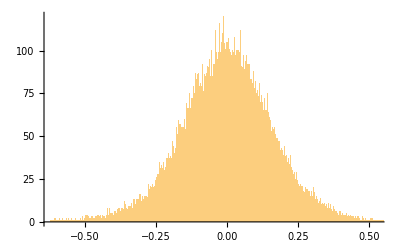

```mathematica
Histogram[Re@offdiag,10000]
```

```mathematica
matdata[[1;;2,2;;$K+1]]
```

```mathematica
Map[Diagonal,matdata[[All,2;;$K+1]],{2}]//Flatten
```

```mathematica
StandardDeviation[($N)/(√($N-1))Map[Diagonal,matdata[[All,2;;$K+1]],{2}]//Flatten]
```

0.368624

```mathematica
unitMats = (#-Tr[#]*IdentityMatrix[9]/9)&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√9),9], 100000];
```

```mathematica
diag = 9/(√(9-1))Map[Diagonal,unitMats]//Flatten//Chop;
```

```mathematica
diag//Length
```

900000

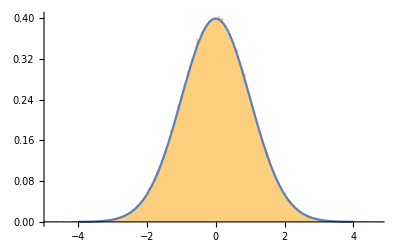

```mathematica
Show[
Histogram[diag, 400, PDF],
Plot[1/(√(2π))Exp[-1/2 x^2], {x, -4, 4}]
]
```

```mathematica
Histo
```

```mathematica
9*10000
```

```mathematica
matdata[[All,2]]//Length
```

10000

```mathematica
simelem =Map[Diagonal,matdata[[All,2;;$K+1]],{2}]//Flatten;
```

```mathematica
unitMats = RandomVariate[GaussianUnitaryMatrixDistribution[1,3], 10000];
```

```mathematica
unitelem =Re[unitMats[[All,1,2]]];
```

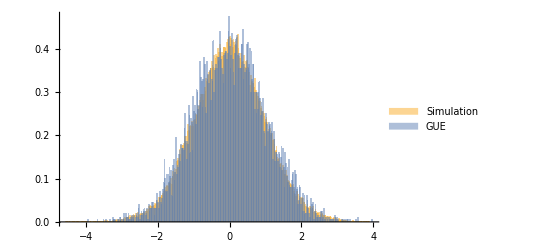

```mathematica
Histogram[{Standardize[simelem],Standardize[unitelem]},300,PDF,ChartLegends->Placed[{"Simulation","GUE"},Below]]
```

```mathematica
GraphicsGrid@ArrayReshape[Table[Histogram[{Standardize[simelem[[All,i,j]]],Standardize[unitelem]},300,PDF,ChartLegends->Placed[{"Simulation","GUE"},Below]],{i,1,3},{j,1,3}],{3,3}]
```

-Graphics-

```mathematica
Re[unitMats[[All,1,2]]]//Length
```

10000

```mathematica
traces = Table[ Tr[MatrixPower[#, n]]&/@matdata[[d]][[All, 2]]//Chop//Re,{d,1,2},{n,6,8}];
```

```mathematica
Table[StandardDeviation[traces[[All, k]]], {k, 1, 3}]
```

```mathematica
Around[#]&/@Table[StandardDeviation[Tr[MatrixPower[#, n]]&/@matdata[[d]][[All, 2]]]//Chop//Re,{n,6,8},{d,1,2}]
```

{0.030410.00017,0.01510.0021,0.01410.0007}

```mathematica
Around[#]&/@StandardDeviation[]
```

{0.0180.024,0.0080.013,0.0070.012}

```mathematica
unitMats = RandomVariate[GaussianUnitaryMatrixDistribution[1,3], 100000];
```

```mathematica
plts = Monitor[Table[Module[{}, (
obsSim[n] = Tr[MatrixPower[#, n]]&/@matdata[[All, 2]]//Chop//Re;
(*obsUnitary[n] = Tr[MatrixPower[#, n]]&/@unitMats//Chop//Re;
*)
Histogram[{Standardize[obsSim[n]](*, Standardize[obsUnitary[n]]*)}, 3000, PDF, ImageSize->500]
)], {n, 2, 13}], ProgressIndicator[(n-2)/(13-2)]];
```

```mathematica
Framed[Column[{Style["Title",Darker@Blue,Bold,16],GraphicsGrid[ArrayReshape[plts,{4,4}],Frame->All,ImageSize->2000]},
Alignment->Center],FrameMargins->10]
```

$Aborted

```mathematica
Export[plotsDir<>"/eigDist-Symplectic.pdf", Rasterize[plt, ImageResolution->300, ImageSize->500]]
```

../../plots/plots-104/eigDist-Symplectic.pdf